# Period Finding with the FFT

Given the set  f_0, f_1,  f_2 ... f_(N-1),  if   f_k=f_(k+ n r) where n is an integer, the function f is said to be periodic with period r. For example, in Fig. 4.1, we plotted a simple function
f:{0,1}^8→{0,1}^1

```mathematica
ClearAll["Global`*"]
num=2^5;
patch={1,0,1,0,0,1,0,0};
flist=Flatten[Table[patch,{k,0,num}]]
```

{1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0}

The above mapping repeats with a period of r=8. A graphical representation of this function is shown below. We could glean the value of r by visual inspection, but that becomes more difficult, and inefficient, as the size of the period r increases.

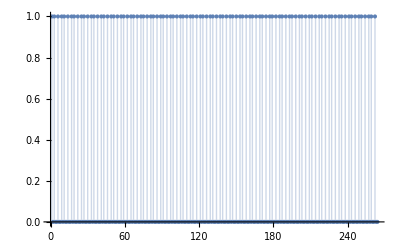

```mathematica
ListPlot[flist,Filling->Axis]
```

However, if we take the FFT of this data, and plot the power spectrum (the square of its absolute value) ,

```mathematica
hlist=Fourier[flist];
```

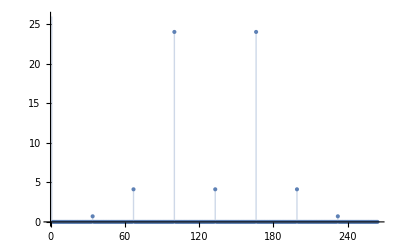

```mathematica
ListPlot[Abs[hlist]^2,Filling->Axis,PlotRange->{0,26}]
```

we find a few discrete peaks at values of the abscissa k={0,32,64,96,128,160,192,224} that correspond to integer multiples of the quantity 1/r, and from which we can quickly estimate the value of r.

### A More Complicated Example

The above example is somewhat artificial as it assumes that the dimension N is an integer multiple of  period r. In general, a periodic function will have an off-set b, a fraction of r , so that  the register dimension N'= m r + b , where m is an integer.

Consider again a case where b=0

```mathematica
num=11;
r=13;
patch=Table[RandomInteger[{0,2^11}],{i,1,r}];
flist1=Join[Flatten[Table[patch,{k,1,num}]]];
ndim1=Dimensions[flist1][[1]]
```

143

Note: by construction, N/r, is an integer.

```mathematica
ndim1/r
```

11

Let’s plot this periodic function

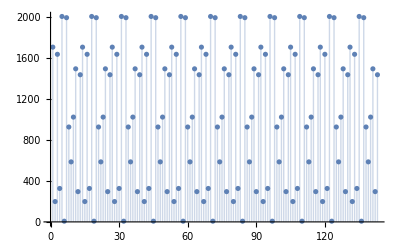

```mathematica
ListPlot[flist1,Filling->Axis]
```

As well as the power spectrum of its discrete Fourier Transform.

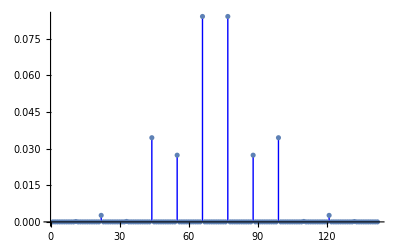

```mathematica
hlist1=Fourier[flist1];
power1=Total[(Abs[hlist1])^2];
normlist1=Chop[(Abs[hlist1])^2/power1];
fig1=ListPlot[Drop[normlist1,1],Filling->Axis,FillingStyle->Blue,PlotRange->All]
```

Again, the non-zero DFT peaks correspond to integral values of 1/r. Let’s itemize below, in tabular form, the values of the index k, in the first column, for which the DFT peaks occur (Here we choose, arbitrarily, peaks whose magnitude > 0.01 ). The second column itemizes the fractions k/N, and the third column r k/N. Inspection of that table again show that the DFT peaks occur at values of k in which the ration k/N
is an integral multiple of 1/r.

```mathematica
klist1=Drop[DeleteDuplicates[Table[If[normlist1[[i]]>0.01,{i-1,(i-1)/ndim1,r (i-1)/ndim1}],{i,1,ndim1}]],2];
MatrixForm[klist1]
```

(44 | 4/13 | 4
55 | 5/13 | 5
66 | 6/13 | 6
77 | 7/13 | 7
88 | 8/13 | 8
99 | 9/13 | 9)

We repeat the above exercise using with the same function with period r given above, but introduce a non-zero off-shift for the register.

```mathematica
remainder=Take[patch,4];
flist2=Join[Flatten[Table[patch,{k,1,num}]],remainder];
(*flist=Flatten[Table[patch,{k,1,num}]];*)
ndim2=Dimensions[flist2][[1]];
```

Now the ratio r/N'

```mathematica
r/ndim2
```

13/147

is no longer an integer. Let’s plot its power spectrum,

```mathematica
hlist2=Fourier[flist2];
power2=Total[(Abs[hlist2])^2];
normlist2=Chop[(Abs[hlist2])^2/power2];
fig2=ListPlot[Style[Drop[normlist2,1],Red],Filling->Axis,FillingStyle->Red,PlotRange->All];
```

which is shown below by the red lines. We superimpose this figure with the ones illustrated above in blue.

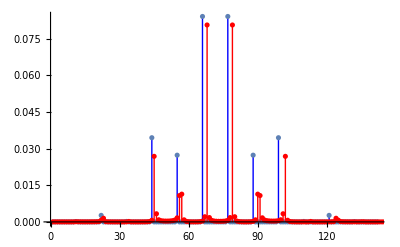

```mathematica
figs=Show[fig1,fig2]
```

Note the similarities, but the red lines do not fall on the values of k for which we can identify integral multiples of 1/r !  To that end we take a short detour and introduce an algorithm that utilizes the continued fraction representation of numbers.

## A Continued Fraction Theorem

A continued fraction represents a number as a series of nested fractions. For example, given number a, its continued fraction representation is given by the expression

Typically, a rational number contains a finite number of coefficients a_n. In Mathematica, these coefficients labeled [a_(0,)a_(1,)a_(2,)...], are obtained with the command

```mathematica
?ContinuedFraction
```

RowBox[{"ContinuedFraction", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["n", "TI"]}], "]"}] generates a list of the first StyleBox["n", "TI"] terms in the continued fraction representation of StyleBox["x", "TI"]. 
RowBox[{"ContinuedFraction", "[", StyleBox["x", "TI"], "]"}] generates a list of all terms that can be obtained given the precision of StyleBox["x", "TI"].

So the continued fraction representation for the number  0.127

```mathematica
y=ContinuedFraction[0.127]
```

{0,7,1,6,1}

terminates at a_4=1.

It is useful to define the nth convergent which is a partial sum for the continued fraction.

```mathematica
?Convergents
```

RowBox[{"Convergents", "[", StyleBox["list", "TI"], "]"}] gives a list of the convergents corresponding to the continued fraction terms StyleBox["list", "TI"].
RowBox[{"Convergents", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the first StyleBox["n", "TI"] convergents for a number StyleBox["x", "TI"].
RowBox[{"Convergents", "[", StyleBox["x", "TI"], "]"}] gives if possible all convergents leading to the number StyleBox["x", "TI"].

So

```mathematica
Convergents[y]
```

{0,1/7,1/8,7/55,8/63}

Provides the successive partial sums, or convergents, of y. In other words, the sum of the first two terms  0+1/7 naturally evaluates to 1/7, the first three terms 0+1/(7+1/1) evaluates to 1/8 and so on. The final convergent 8/63=0.126984,

### An Important Theorem

Consider a real number y and the rational fraction k/r where both k,r are positive integers, and 1
| y - k/r | ≤ 1/2 r^2,
	1G. H. Hardy and E. M. Wright, page 153, An Introduction to the Theory of Numbers, 4the ed., Oxford U. Press (1963)
then the continued fraction expansion of y contains, in its list of convergents, an integral multiple of 1/r

Example:
Suppose r1=3, k/r1=2/3,  and y=0.65.  Let's first make sure that the above inequality is satisfied

```mathematica
y=0.65;k=2;r1=3;
```

```mathematica
Abs[y-k/r1]≤1/4/r1^2
```

True

Since the equality is satisfied, construct the convergents of y

```mathematica
Convergents[y]
```

{0,1,1/2,2/3,13/20}

Notice that the fourth entry 2/3  is indeed a multiple of 1/r = 1/3. Furthermore, if we know the bound on r, then the convergent with the largest denominator <r, is the sought for fraction.

Exercise: Try  this for different values of r and y

### Application of the Continued Fraction Theorem to Period Finding

Inspecting our composite figure;

```mathematica
figs
```

-Graphics-

we find that some of the red peaks align closely with the blue ones. The blue peaks represent the values of k in which the ratio k/N  (where N=m r, and m is an integer, is the dimension of the register) is an integral multiple of 1/r. The red lines represent peaks at values of k shifted from the latter because an integral multiple of r is not a divisor of the new register size N' = m r +b, where b is an off-set value. We can estimate, using the continued fraction method the values of k/r, for the red shifted lines by constructing the convergents of y=k/N'.

So lets find the values of y=k/N' and list those values. They are listed below in the format {k,k/N'}.

```mathematica
klist2=Drop[DeleteDuplicates[Table[If[normlist2[[i]]>0.01,{i-1,(i-1)/ndim2}],{i,1,ndim2}]],2]
kdim=Dimensions[klist2][[1]];
```

{{45,15/49},{56,8/21},{57,19/49},{68,68/147},{79,79/147},{90,30/49},{91,13/21},{102,34/49}}

```mathematica
convergentlist=Drop[DeleteDuplicates[Table[If[normlist2[[i]]>0.01,{i-1,Convergents[(i-1)/ndim2]}],{i,1,ndim2}]],2];
```

```mathematica
Style[MatrixForm[convergentlist],FontSize->16]
```

(45 | {0,1/3,3/10,4/13,15/49}
56 | {0,1/2,1/3,2/5,3/8,8/21}
57 | {0,1/2,1/3,2/5,5/13,7/18,19/49}
68 | {0,1/2,6/13,31/67,68/147}
79 | {0,1,1/2,7/13,36/67,79/147}
90 | {0,1,1/2,2/3,3/5,8/13,11/18,30/49}
91 | {0,1,1/2,2/3,3/5,5/8,13/21}
102 | {0,1,2/3,7/10,9/13,34/49})

Exercise: From this table read off the convergents, and the index k, in which the denominator of the latter is an integral value of 1/r.

Exercise: Repeat the above steps leading to the composite figures, for different values of r ? How does your success rate depend on the values for r, the off-set and register size ?

# Miller’s Algorithm

In notebook 4.4 we discuss the RSA encryption protocol. The key to breaking it involves factoring a semi-prime number n, a product of two prime numbers p,q. Miller’s algorithm is a classical probabilistic algorithm which we describe below. A key feature of the latter is finding the period of a function

Lets first construct a semi-prime number

```mathematica
p=Prime[RandomInteger[{1,11}]];
q=Prime[RandomInteger[{1,11}]];
n= p q
```

203

Our goal is to factor it into its prime components. The first step is constructing the function f(r) and finding its period. The latter is defined as
 f(r) = s^r Mod n

where s is an arbitrary integer, called the seed, so that 1≤s ≤ n, and s should be coprime with n (i.e. GCD[n,s]=1). 
If it is not, then you have already found a factor of n. Abort algorithm.

```mathematica
(* pick a random seed *)
s=RandomInteger[{1,n}];
(* check its greatest common divisor with n *)
GCD[s,n];
If[GCD[s,n]≠ 1,Print[" Found factor ",GCD[s,n]];Abort[]]
```

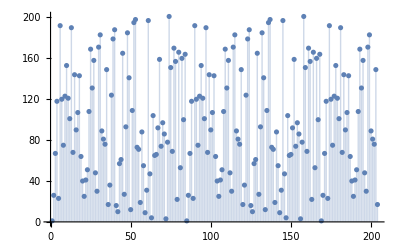

```mathematica
(* now construct the function f(r) *)
f=Table[Mod[s^r,n],{r,0,n}];
ListPlot[f,Filling->Axis]
rlist=Cases[Table[If[f[[i]]==1,i],{i,1,n}],_Integer];
```

Note that the above graph illustrates a periodic function. Below, we find its period by brute force (i.e. we do not use FFT as above). The value
of ω is the first given by the solution  of s^ω ≡ 1 Mod n   which is equivalent to  s^ω-1 ≡0 Mod n, or   if ω is an even number  (s^(ω/2)-1)(s^(ω/2)+1) ≡ 0 Mod n, but that is equivalent to the statement that (s^(ω/2)-1)(s^(ω/2)+1) = p q M   where M is an integer. Or,  ((s^(ω/2)-1)(s^(ω/2)+1))/(p q)  is an integer.  Unless s^(ω/2) ≡±1, this factor implies that either of the factors  (s^(ω/2)±1) must have p or q as a common factor. Therefore the greatest common divisor (GCD) of these factor will results in at least one of the p or q.

```mathematica
(* evaluate the period of f(r) *)
period=rlist[[2]]-rlist[[1]];
Print[" ω = ",period]
```

ω = 84

```mathematica
(* check if ω is an even number; check if s^(ω/2) ≢ ±1 Mod n. If these checks fail try again with another seed *)
```

```mathematica
If[OddQ[period],Print["Stop algorithm try new s"];Abort[]]
If[Mod[s^period/2,n]==1,Print["Stop algorithm try new s"];Abort[]]
If[Mod[s^period/2,n]==n-1,Print["Stop algorithm try new s"];Abort[]]
```

```mathematica
Print["gcd[s^(r/2)+1,n] = ",GCD[s^(period/2)+1,n]]
Print["gcd[s^(r/2)-1,n] = ",GCD[s^(period/2)-1,n]]
```

gcd[s^(r/2)+1,n] = 29

gcd[s^(r/2)-1,n] = 7

```mathematica
Print["p = ",p,"  "," q = ",q]
```

p = 29   q = 7

Try a few cases yourself with different n, s.